```mathematica
Fav= 1/5(1+(Cos[Sqrt[(B1/2)^2+(δBz/2)^2]*tg]-(B1/(2*Sqrt[(B1/2)^2+(δBz/2-A/2)^2]))*Sin[Sqrt[(B1/2)^2+(δBz/2-A/2)^2]*tg]*Cos[A/2*tg])^2)
```

1/5 (1+(Cos[tg √(B1^2/4+δBz^2/4)]-(B1 Cos[(A tg)/2] Sin[tg √(B1^2/4+(-A/2+δBz/2)^2)])/(2 √(B1^2/4+(-A/2+δBz/2)^2)))^2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
Fav1=Fav*1/Sqrt[2*π*σ^2]*Exp[-1/2*(δBz/σ)^2]/.tg->(π/B1)
```

(ⅇ^(-δBz^2/(2 σ^2)) (1+(Cos[(π √(B1^2/4+δBz^2/4))/B1]-(B1 Cos[(A π)/(2 B1)] Sin[(π √(B1^2/4+(-A/2+δBz/2)^2))/B1])/(2 √(B1^2/4+(-A/2+δBz/2)^2)))^2))/(5 √(2 π) √(σ^2))

```mathematica
Fav2=Fav1/.{A->1,B1->1,σ->1}
```

(ⅇ^(-δBz^2/2) (1+(Cos[π √(1/4+δBz^2/4)]-(0.311406 Sin[π √(1/4+(-1/2+δBz/2)^2)])/(√(1/4+(-1/2+δBz/2)^2)))^2))/(5 √(2 π))

```mathematica
Integrate[Fav2,δBz]
```

(∫ⅇ^(-δBz^2/2) (1+(Cos[π √(1/4+δBz^2/4)]-(0.311406 Sin[π √(1/4+(-1/2+δBz/2)^2)])/(√(1/4+(-1/2+δBz/2)^2)))^2)ⅆδBz)/(5 √(2 π))

```mathematica
Integrate[Fav2,{δBz,-100,100}]
```

∫_-100^100 (ⅇ^(-δBz^2/2) (1+(Cos[π √(1/4+δBz^2/4)]-(0.311406 Sin[π √(1/4+(-1/2+δBz/2)^2)])/(√(1/4+(-1/2+δBz/2)^2)))^2))/(5 √(2 π))ⅆδBz

```mathematica
i1=Cos[c]^2*2/n*π*Sqrt[4*c^2/(4*c^2-n*π)]Exp[-(b^2*(4*c^2/(n*π)-1))/(2*σ^2)]
```

(4 ⅇ^(-(b^2 (-1+(4 c^2)/(n π)))/(2 σ^2)) π √(c^2/(4 c^2-n π)) Cos[c]^2)/n

```mathematica
Integrate[i1,c]
```

(4 π ∫ⅇ^(-(b^2 (-1+(4 c^2)/(n π)))/(2 σ^2)) √(c^2/(4 c^2-n π)) Cos[c]^2ⅆc)/n

```mathematica
Integrate[Fav2,{δBz,-100,100}]
```

0.31868

```mathematica
Fav2
```

((1+Cos[π √(1/4+δBz^2/4)]^2) exp[-δBz^2/(2 σ^2)])/(5 √(2 π) √(σ^2))

```mathematica
test=(Cos[x])^2;
Integrate[test,x]
```

x/2+1/4 Sin[2 x]

```mathematica
test2=(1/(x^2+ax+b))*e^(-x^2)
```

(e^(-x^2))/(ax+b+x^2)

```mathematica
Integrate[test2,x]
```

∫(e^(-x^2))/(ax+b+x^2)ⅆx

```mathematica
Integrate[test2,{x,-∞,∞}]
```

ConditionalExpression[(e^(ax+b) π Erfc[√(ax+b) √Log[e]])/(√(ax+b)), Re[Log[e]]>0&&((ax+b∉ℝ&&Im[ax]+Im[b]≠0)||Re[ax+b]≥0)]

```mathematica
Fav3=Fav/.{δBz->0,tg->(π/B1)}
```

1/5 (1+(Cos[(√(B1^2) π)/(2 B1)]-(B1 Cos[(A π)/(2 B1)] Sin[(√(A^2/4+B1^2/4) π)/B1])/(2 √(A^2/4+B1^2/4)))^2)

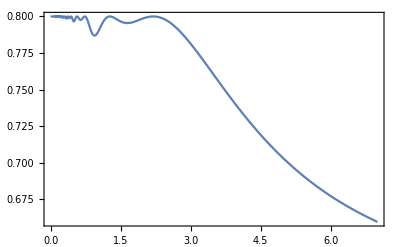

```mathematica
Plot[1-Fav3/.A->2.2,{B1,0,7},Frame->True]
```